```mathematica
ClearAll["Global`*"]
```

```mathematica
table081 = Import["C:\\Users\\tatki\\Documents\\PHOTONICS\\YEAR 4\\Heat transfer\\TV\\Kinetic0,8_1.txt",{"Table", "Data"}];
table081[[All,1]]=table081[[All,1]]-table081[[1,1]];
table081[[All,2]]=((table081[[All,2]]+0.002)/(0.0043×0.0094));
table081[[All,2]]=table081[[All,2]]-Min[table081[[All,2]]];
```

```mathematica
table082 = Import["C:\\Users\\tatki\\Documents\\PHOTONICS\\YEAR 4\\Heat transfer\\TV\\Kinetic0,8_2.txt",{"Table", "Data"}];
table082[[All,1]]=table082[[All,1]]-table082[[1,1]];
table082[[All,2]]=((table082[[All,2]]+0.002)/(0.0043×0.0094));
table082[[All,2]]=table082[[All,2]]-Min[table082[[All,2]]];
```

```mathematica
table083 = Import["C:\\Users\\tatki\\Documents\\PHOTONICS\\YEAR 4\\Heat transfer\\TV\\Kinetic0,8_3.txt",{"Table", "Data"}];
table083[[All,1]]=table083[[All,1]]-table083[[1,1]];
table083[[All,2]]=((table083[[All,2]]+0.002)/(0.0043×0.0094));
table083[[All,2]]=table083[[All,2]]-Min[table083[[All,2]]];
```

```mathematica
table084 = Import["C:\\Users\\tatki\\Documents\\PHOTONICS\\YEAR 4\\Heat transfer\\TV\\Kinetic0,8_4.txt",{"Table", "Data"}];
table084[[All,1]]=table084[[All,1]]-table084[[1,1]];
table084[[All,2]]=((table084[[All,2]]+0.002)/(0.0043×0.0094));
table084[[All,2]]=table084[[All,2]]-Min[table084[[All,2]]];
```

```mathematica
table085 = Import["C:\\Users\\tatki\\Documents\\PHOTONICS\\YEAR 4\\Heat transfer\\TV\\Kinetic0,8_5.txt",{"Table", "Data"}];
table085[[All,1]]=table085[[All,1]]-table085[[1,1]];
table085[[All,2]]=((table085[[All,2]]+0.002)/(0.0043×0.0094));
table085[[All,2]]=table085[[All,2]]-Min[table085[[All,2]]];
```

```mathematica
Export["table081.dat",table081];Export["table082.dat",table082];Export["table083.dat",table083];Export["table084.dat",table084];Export["table085.dat",table085];
```

```mathematica
T[k_,T0_,Tout_,t_]:=Tout+(T0-Tout)×Exp[-k×t]
```

```mathematica
fit081=FindFit[table081,T[k,T0,Tout,t],{k,T0, Tout},t,MaxIterations->1000]
```

{k→0.0407611,T0→39.2479,Tout→0.019285}

```mathematica
fit082=FindFit[table082,T[k,T0,Tout,t],{k,T0, Tout},t,MaxIterations->1000]
```

{k→0.0478747,T0→37.3007,Tout→-0.00211381}

```mathematica
fit083=FindFit[table083,T[k,T0,Tout,t],{k,T0, Tout},t,MaxIterations->1000]
```

{k→0.0112708,T0→37.4163,Tout→-10.2241}

```mathematica
fit084=FindFit[table084,T[k,T0,Tout,t],{k,T0, Tout},t,MaxIterations->1000]
```

{k→0.0475006,T0→35.0374,Tout→-2.15174}

```mathematica
fit085=FindFit[table085,T[k,T0,Tout,t],{k,T0, Tout},t,MaxIterations->1000]
```

{k→0.125978,T0→66.3384,Tout→18.7816}

```mathematica
T0set={T0/.fit081,T0/.fit082,T0/.fit083,T0/.fit084}
```

{39.2479,37.3007,37.4163,35.0374}

```mathematica
Toset={Tout/.fit081,Tout/.fit082,Tout/.fit083,Tout/.fit084}
```

{0.019285,-0.00211381,-10.2241,-2.15174}

```mathematica
Mean[Toset]
```

-3.08966

```mathematica
StandardDeviation[Toset]
```

4.86408

```mathematica
k081=Mean[{k/.fit081,k/.fit082,k/.fit083,k/.fit084}]
```

0.0368518

```mathematica
StandardDeviation[{k/.fit081,k/.fit082,k/.fit083,k/.fit084}]
```

0.0173644

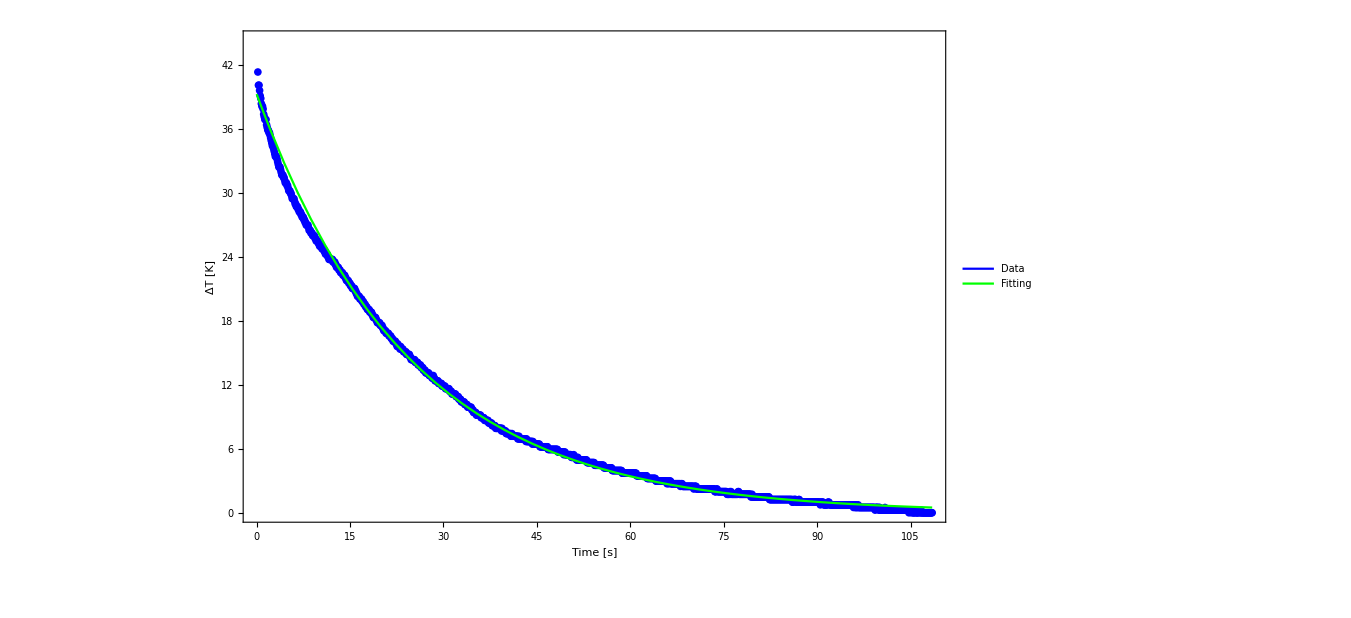

```mathematica
Legended[Show[ListPlot[table081,PlotStyle->Blue],
Plot[T[k,T0,Tout,t]/.fit081,{t,0,Max[table081[[All,1]]]},PlotStyle->Green],  Frame->{True,True,False,False},FrameLabel->{"Time [s]","ΔT [K]"},ImageSize->1000, BaseStyle->{FontSize->24}],LineLegend[{Blue, Green},{"Data", "Fitting"}]]
```